```mathematica
P[n_,k_,j_] := (-1)^(k+1)/k+P[Floor[n/j],k+1,Floor[n/j]]+P[n,k,j-1]
P[n_,k_,1] := 0
```

```mathematica
P[100,1,100]
```

428/15

```mathematica
P[n,1,n]
```

$Aborted

```mathematica
P[100,1,50]
```

-322/15

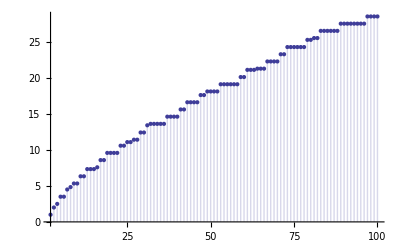

```mathematica
DiscretePlot[ Abs[P[n,1,n]],{n,2,100}]
```

```mathematica
P[101,k,101]
```

(100 (-1)^(1+k))/k+(283 (-1)^(2+k))/(1+k)+(324 (-1)^(3+k))/(2+k)+(184 (-1)^(4+k))/(3+k)+(51 (-1)^(5+k))/(4+k)+(7 (-1)^(6+k))/(5+k)

```mathematica
S[k_] := P[100,k,100]-P[99,k,99]
```

```mathematica
S[1.000001]
```

-2.08333×10^-7-6.53609×10^-13 ⅈ

```mathematica
P[100,k,100]
```

(99 (-1)^(1+k))/k+(283 (-1)^(2+k))/(1+k)+(324 (-1)^(3+k))/(2+k)+(184 (-1)^(4+k))/(3+k)+(51 (-1)^(5+k))/(4+k)+(7 (-1)^(6+k))/(5+k)

```mathematica
P[99,k,99]
```

(98 (-1)^(1+k))/k+(276 (-1)^(2+k))/(1+k)+(312 (-1)^(3+k))/(2+k)+(178 (-1)^(4+k))/(3+k)+(51 (-1)^(5+k))/(4+k)+(7 (-1)^(6+k))/(5+k)

```mathematica
T[n_] := P[n,k,n]
```

```mathematica
T[99]
```

(98 (-1)^(1+k))/k+(276 (-1)^(2+k))/(1+k)+(312 (-1)^(3+k))/(2+k)+(178 (-1)^(4+k))/(3+k)+(51 (-1)^(5+k))/(4+k)+(7 (-1)^(6+k))/(5+k)

```mathematica
T[120]
```

(119 (-1)^(1+k))/k+(363 (-1)^(2+k))/(1+k)+(453 (-1)^(3+k))/(2+k)+(284 (-1)^(4+k))/(3+k)+(86 (-1)^(5+k))/(4+k)+(7 (-1)^(6+k))/(5+k)

```mathematica
V[n_, k_ ] := Sum[ ((-1)^(k+1))/k + V[n/j, k+1],{j,2,n}]
```

```mathematica
V[100,k]
```

(99 (-1)^(1+k))/k+(283 (-1)^(2+k))/(1+k)+(324 (-1)^(3+k))/(2+k)+(184 (-1)^(4+k))/(3+k)+(51 (-1)^(5+k))/(4+k)+(7 (-1)^(6+k))/(5+k)

```mathematica
3+3I
```

3+3 ⅈ

```mathematica
Re[V[100,.5]]
```

-3.42012×10^-14

```mathematica
Table[ N[Im[P[n,1I,n]-P[n-1,1I,n-1]]], {n,2,100}]
```

{0.0432139,0.0432139,0.021607,0.0432139,-1.38778×10^-17,0.0432139,0.00864278,0.021607,-1.38778×10^-17,0.0432139,-0.0172856,0.0432139,-1.38778×10^-17,-1.38778×10^-17,-1.04083×10^-17,0.0432139,-0.0172856,0.0432139,-0.0172856,-1.38778×10^-17,-1.38778×10^-17,0.0432139,-0.0259284,0.021607,-1.38778×10^-17,0.00864278,-0.0172856,0.0432139,-0.0345711,0.0432139,-0.00610079,-1.38778×10^-17,-1.38778×10^-17,-1.38778×10^-17,-0.0302497,0.0432139,-1.38778×10^-17,-1.38778×10^-17,-0.0259284,0.0432139,-0.0345711,0.0432139,-0.0172856,-0.0172856,-1.38778×10^-17,0.0432139,-0.0305039,0.021607,-0.0172856,-1.38778×10^-17,-0.0172856,0.0432139,-0.0259284,-1.38778×10^-17,-0.0259284,-1.38778×10^-17,-1.38778×10^-17,0.0432139,-0.0432139,0.0432139,-1.38778×10^-17,-0.0172856,-0.0105591,-1.38778×10^-17,-0.0345711,0.0432139,-0.0172856,-1.38778×10^-17,-0.0345711,0.0432139,-0.0350795,0.0432139,-1.38778×10^-17,-0.0172856,-0.0172856,-1.38778×10^-17,-0.0345711,0.0432139,-0.0305039,-1.04083×10^-17,-1.38778×10^-17,0.0432139,-0.0432139,-1.38778×10^-17,-1.38778×10^-17,-1.38778×10^-17,-0.0259284,0.0432139,-0.0432139,-1.38778×10^-17,-0.0172856,-1.38778×10^-17,-1.38778×10^-17,-1.38778×10^-17,-0.0328504,0.0432139,-0.0172856,-0.0172856,-0.0302497}

```mathematica
M[n_,k_,j_] := (-1)^(k+1)+M[n/j,k+1,Floor[n/j]]+M[n,k,j-1]
M[n_,k_,1] := 0
```

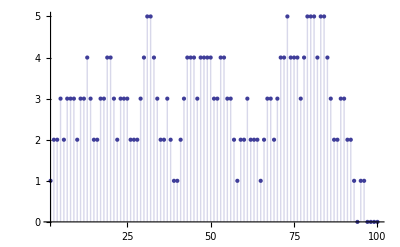

```mathematica
DiscretePlot[ Abs[M[n,2.5,n]],{n,2,100}]
```

```mathematica
N[M[88,1+I,88]]
```

0.0864278+3.70453×10^-17 ⅈ

```mathematica
P2[n_,k_,j_] := j((-1)^(k+1)/k+P2[Floor[n/j],k+1,Floor[n/j]])+P2[n,k,j-1]
P2[n_,k_,1] := 0
```

```mathematica
P2[100,1,100]
```

292149953504274361788974787095433526022627/139440750459424954329067617870624607113600

```mathematica
P3[n_, k_] := Sum[j((-1)^(k+1)/k + P3[Floor[n/j],k+1]),{j,2,n}]
```

```mathematica
P3[100,1]
```

69389/60

```mathematica
P3[99,1]
```

69389/60

```mathematica
Expand[P2[100,k,100]]
```

(5049 (-1)^(1+k))/k+(16780 (-1)^(2+k))/(1+k)+(21426 (-1)^(3+k))/(2+k)+(13441 (-1)^(4+k))/(3+k)+(4112 (-1)^(5+k))/(4+k)+(640 (-1)^(6+k))/(5+k)

```mathematica
P4[n_,k_,j_, a_] := j^a((-1)^(k+1)/k+P4[Floor[n/j],k+1,Floor[n/j],a])+P4[n,k,j-1,a]
P4[n_,k_,1,a_] := 0
```

```mathematica
N[P4[100,1,100,I]]
```

-15.2228-6.06391 ⅈ

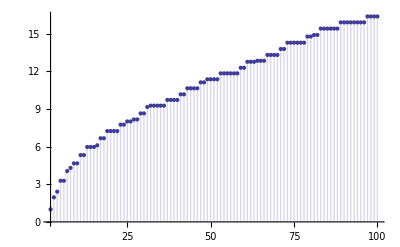

```mathematica
DiscretePlot[Abs[P4[n,1,n,I]],{n,2,100}]
```

```mathematica
Table[N[Abs[P4[n,1,n,I]]-Abs[P4[n-1,1,n-1,I]]],{n,2,100}]
```

{1.,0.95904,0.452594,0.867604,0.,0.775158,0.253034,0.361793,8.88178×10^-16,0.662151,-8.88178×10^-16,0.64353,8.88178×10^-16,8.88178×10^-16,0.135927,0.56273,8.88178×10^-16,0.572853,-8.88178×10^-16,-8.88178×10^-16,1.77636×10^-15,0.509893,0.,0.25518,-1.77636×10^-15,0.160927,0.,0.482207,-3.55271×10^-15,0.511384,0.106546,0.,0.,0.,3.55271×10^-15,0.455764,0.,3.55271×10^-15,-3.55271×10^-15,0.446087,-1.77636×10^-15,0.481048,7.10543×10^-15,-3.55271×10^-15,-1.77636×10^-15,0.475359,-3.55271×10^-15,0.245451,-3.55271×10^-15,3.55271×10^-15,0.,0.472611,3.55271×10^-15,0.,0.,0.,0.,0.443995,-8.88178×10^-15,0.478449,-3.55271×10^-15,3.55271×10^-15,0.0786341,3.55271×10^-15,-7.10543×10^-15,0.466536,-3.55271×10^-15,0.,0.,0.473867,-7.10543×10^-15,0.504785,3.55271×10^-15,-8.88178×10^-15,0.,5.32907×10^-15,-3.55271×10^-15,0.488939,-5.32907×10^-15,0.124856,0.,0.509364,-7.10543×10^-15,7.10543×10^-15,-5.32907×10^-15,-1.77636×10^-15,7.10543×10^-15,0.497493,-1.77636×10^-15,3.55271×10^-15,-1.77636×10^-15,-3.55271×10^-15,-5.32907×10^-15,3.55271×10^-15,5.32907×10^-15,0.470298,0.,-3.55271×10^-15,0.}

```mathematica
PS[n_,k_,j_] := 1/k-PS[Floor[n/j],k+1,Floor[n/j]]+PS[n,k,j-1]
PS[n_,k_,1] := 0
```

```mathematica
PS[100,1,100]
```

428/15

```mathematica
PS[n,1,n] - PS[n-1,1,n-1]
```

$Aborted

```mathematica
PS[n,1,n]
```

$Aborted

```mathematica
F[n_] := PS[n,1,n] - PS[n-1,1,n-1]
```

```mathematica
F[101]
```

1

```mathematica
F2[n_] := PS[n,1,n-1] - PS[n-1,1,n-2]
```

```mathematica
F2[1]
```

0

```mathematica
Table[F2[n],{n,3,100}]
```

{1,1/2,1,0,1,1/3,1/2,0,1,0,1,0,0,1/4,1,0,1,0,0,0,1,0,1/2,0,1/3,0,1,0,1,1/5,0,0,0,0,1,0,0,0,1,0,1,0,0,0,1,0,1/2,0,0,0,1,0,0,0,0,0,1,0,1,0,0,1/6,0,0,1,0,0,0,1,0,1,0,0,0,0,0,1,0,1/4,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0}

```mathematica
P[100,k,100] - P[100,k+1,100]
```

(99 (-1)^(1+k))/k+(184 (-1)^(2+k))/(1+k)+(41 (-1)^(3+k))/(2+k)-(140 (-1)^(4+k))/(3+k)-(133 (-1)^(5+k))/(4+k)-(44 (-1)^(6+k))/(5+k)-(7 (-1)^(7+k))/(6+k)